```mathematica
NotebookEvaluate[NotebookDirectory[]<>"/split_step.nb"];
```

GPE solver v1.4, RZ 2019

```mathematica
defaultscale=8;
HarmonicTrap1D[];
sizes={1024};
k=0;
contactInteractionFactor=4 Pi k;
initialize[];
gridReport
```

sizes | dim | len | max | min | delta | deltak | maxk
{1024} | 1 | 1024 | {8} | {-8} | {16/1023} | {(1023 π)/8192} | {(1023 π)/16}

```mathematica
res={};
do[ts_]:=Module[{},
timeStep=ts;
initialize[];reset;
evolve["ite",100 ,10];
AppendTo[res,Join[{timeStep},energies,{psi}]];
];
doall:={
do[0.0001];
do[0.000316];
do[0.001];
do[0.00316];
do[0.01];
do[0.0316];
do[0.1];
};
```

```mathematica
testGSenergy:=Module[{refE,l,f},
refE=res[[1,2]];
l=Sort@Map[#-{0,refE}&,res[[All,{1,2}]]];
Print[ListLogLogPlot[l]];
l=Log[Drop[l,1]];
f=Fit[l,{1,x},x];
Print[f];
];
testVirial:=Module[{l,f},
l=Sort@res[[All,{1,6}]];
l=Abs[l];
Print[ListLogLogPlot[l]];
l=Log[Drop[l,1]];
f=Fit[l,{1,x},x];
Print[f];
];
testWFn:=Module[{psi0,l,f},
psi0=res[[1,-1]];
l=Sort@Table[{res[[i,1]],NIntegrate[(Abs[res[[i,-1]][x]]^2-Abs[psi0[x]]^2)^2,{x,-8,8}]},{i,Length[res]}];
Print[ListLogLogPlot[l]];
l=Log[Drop[l,1]];
f=Fit[l,{1,x},x];
Print[f];
];
```

```mathematica
res={};
algorithm="firstOrder";
k=0;
contactInteractionFactor=4 Pi k;
initialize[];
reset;
doall;
```

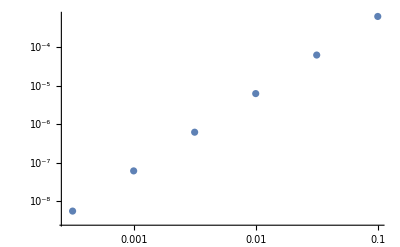

-2.72075+2.01378 x

```mathematica
testGSenergy
```

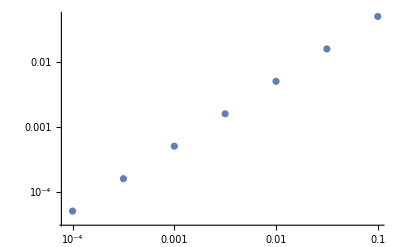

-0.693147+1. x

```mathematica
testVirial
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

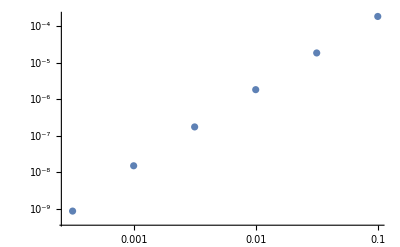

-3.59766+2.10851 x

```mathematica
testWFn
```

```mathematica
res={};
algorithm="secondOrder";
k=0;
contactInteractionFactor=4 Pi k;
initialize[];
reset;
doall;
```

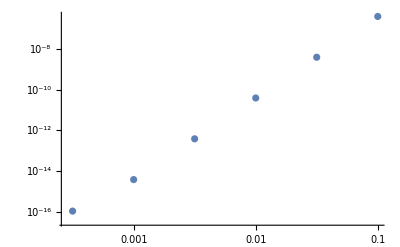

-6.04503+3.87008 x

```mathematica
testGSenergy
```

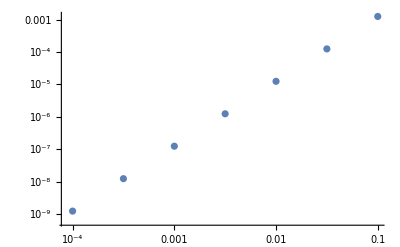

-2.08053+1.99983 x

```mathematica
testVirial
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

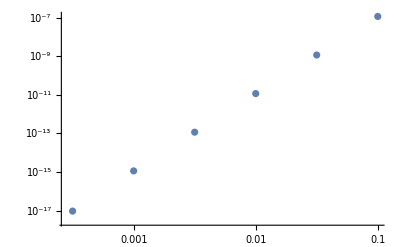

-6.64947+4.02736 x

```mathematica
testWFn
```

```mathematica
res={};
algorithm="firstOrder";
k=-0.2;
contactInteractionFactor=4 Pi k;
initialize[];
reset;
doall;
```

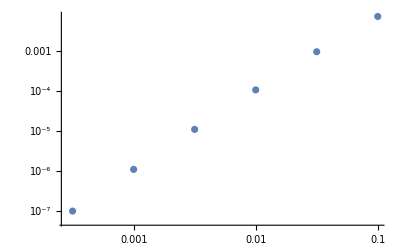

-0.279803+1.94691 x

```mathematica
testGSenergy
```

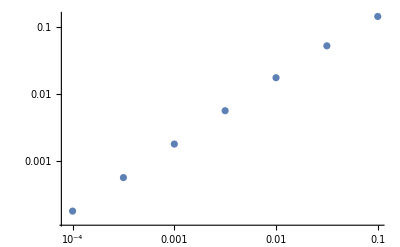

0.343469+0.965036 x

```mathematica
testVirial
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

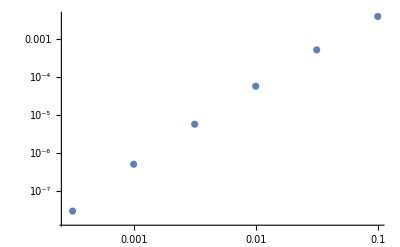

-0.526024+2.04552 x

```mathematica
testWFn
```

```mathematica
res={};
algorithm="secondOrder";
k=-0.2;
contactInteractionFactor=4 Pi k;
initialize[];
reset;
doall;
```

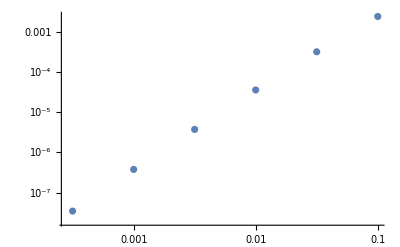

-1.3588+1.94779 x

```mathematica
testGSenergy
```

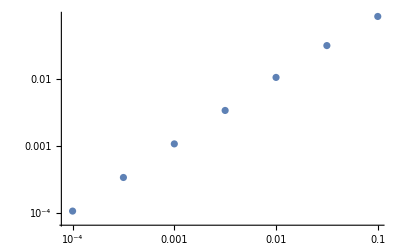

-0.189811+0.962277 x

```mathematica
testVirial
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

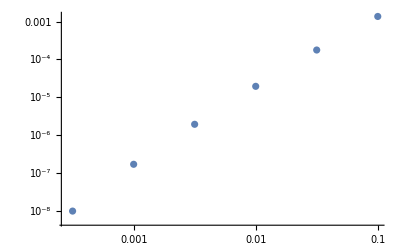

-1.60974+2.04661 x

```mathematica
testWFn
```